```mathematica
e1={1,0};
e2={1/2,Sqrt[3]/2};
p1={0,0};
p2[t_,s_]:=t e1+s e2;
p3[t_,s_]:= -s e1+(t+s) e2;
pcenter[t_,s_]=(p1+p2[t,s]+p3[t,s])/3;
tri[m_,n_,x1_,x2_]:=Line[{m x1+n x2,(m+1) x1+n x2,m x1+(n +1)x2,m x1+n x2}];
point[m_,n_,x1_,x2_]:=Point[{m x1+n x2}];
mm0=9;
nn0=9;
ss=Table[tri[m,n,e1,e2],{m,-mm0+2,mm0},{n,-nn0+2,nn0}];tt=Table[poi[m,n,e1,e2],{m,-mm0+5,mm0},{n,-nn0+10,nn0}];
```

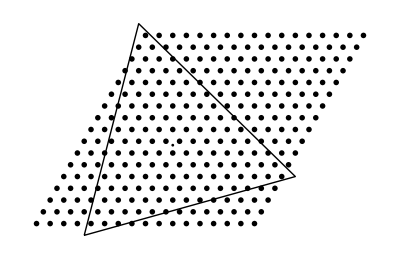

```mathematica
(*l2=Graphics[{Thick,Line[{p1,pcenter[ii,jj],p2[ii,jj]}]}]*)
ii=13;
jj=5;
plcenter=Graphics[{PointSize[0.005],Point[pcenter[ii,jj]]}];
plpoints=Graphics[{PointSize[0.003],tt}];
plottriangles=Graphics[{Thin,ss}];

l1=Graphics[{Thick,Line[{p1,p2[ii,jj],p3[ii,jj],p1}]}];

plot1=Graphics[Point[{p1,p2[ii,jj],p3[ii,jj]}]];
possiblenodes=Table[poi[m,n,e1,e2],{n,1,jj+ii-1},{m,-jj+1,ii-1}];
plotpospoi=Graphics[{PointSize[0.01],possiblenodes}];

(*res=Show[plot0,plot1,l1,l2,plpoi,plcenter,plotpospoi]*)
res=Show[plpoints,l1,plcenter,plotpospoi]
```

```mathematica
eq[x_,y_]={t1 p1[[1]]+ t2 p2[ii,jj][[1]]+t3 p3[ii,jj][[1]]==x,t1 p1[[2]]+ t2 p2[ii,jj][[2]]+t3 p3[ii,jj][[2]]==y,t1+t2+t3==1};
form={t1,t2,t3}/. Solve[eq[x,y],{t1,t2,t3}]//Flatten;
icount=0;iicount=0;
deter=ii^2+ii*jj+jj^2;
(*Print["determinant = ",deter]*)
insidelist={};insidelist2={};
For[m=-jj+1,m≤ ii-1,m++,
For[n=1,n≤ jj+ii-1,n++,
cp=m e1+n e2;

tt1=form[[1]]/. {x-> cp[[1]],y-> cp[[2]]};
tt2=form[[2]]/. {x-> cp[[1]],y-> cp[[2]]};
tt3=form[[3]]/. {x-> cp[[1]],y-> cp[[2]]};

tts1=(deter-m ii-n(ii+jj))/deter;
tts2=(m(ii+jj)+n jj)/deter;
tts3=(-m jj+n ii)/deter;

ttt1=(jj^2+m(jj-ii)+jj*ii+ii^2-n(jj+2ii))/deter;
ttt2=(2m jj+n jj+(m-n) ii)/deter;
ttt3=3(n ii-m jj)/deter;

If[ttt1==0∨ttt2==0∨ttt3==0, Print["t1=",ttt1," t2=",ttt2," t3=",ttt3," ",m," ",n] ];
If[tt1≥ 0&&tt2≥ 0 &&tt3≥ 0,icount=icount+1];
If[tt1≥ 0&&tt2≥ 0 &&tt3≥ 0,insidelist=Join[insidelist,{{m,n}}]];
If[ttt1≥ 0&&ttt2≥ 0 &&ttt3≥ 0,insidelist2=Join[insidelist2,{{m,n}}]];
If[ttt1> 0&&ttt2> 0 &&ttt3> 0,iicount=iicount+1];

]
]
Print["Number of interior nodes = ",iicount]
```

Number of interior nodes = 43

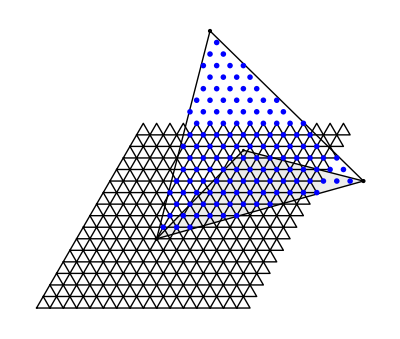

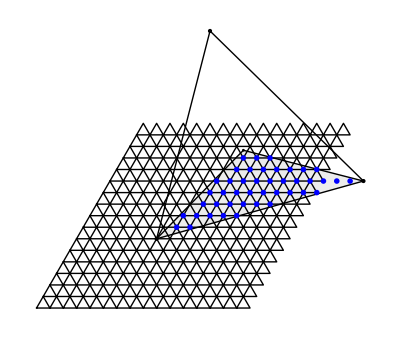

```mathematica
insideNodes14a=Table[poi[insidelist[[k]][[1]],insidelist[[k]][[2]],e1,e2],{k,1,Length[insidelist]}];plotInsideNodes=Graphics[{PointSize[0.01],Blue,insideNodes14a}];
insideNodes14b=Table[poi[insidelist2[[k]][[1]],insidelist2[[k]][[2]],e1,e2],{k,1,Length[insidelist2]}];
tri=Graphics[{Gray,Opacity[0.15],Polygon[{p1,pcenter[ii,jj],p2[ii,jj]}]}];plotInsideNodes2=Graphics[{PointSize[0.01],Blue,insideNodes14b}];res=Show[tri,plot0,plot1,l1,l2,plpoi,plcenter,plotInsideNodes]
res2=Show[tri,plot0,plot1,l1,l2,plpoi,plcenter,plotInsideNodes2]
```

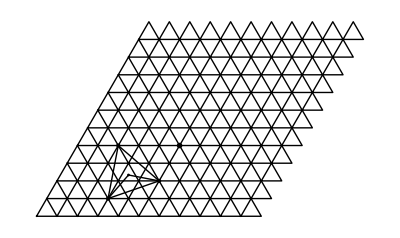

```mathematica
tst62=Graphics[{PointSize[0.01],poi[6,2,e1,e2]}];
tst65=Graphics[{PointSize[0.01],poi[2,3,e1,e2]}];
tst31=Graphics[{PointSize[0.01],poi[5,2,e1,e2]}];

res3=Show[plot0,plot1,l1,l2,plpoi,plcenter,tst65]
```

```mathematica
rfdata=Import["rfd.dat"];
```

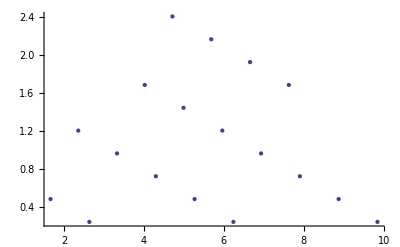

```mathematica
rfdplt=ListPlot[rfdata]
```

```mathematica
3 18+2 + 2
```

58

```mathematica
?Line
```

Line[{pt_1,pt_2,…}] is a graphics primitive which represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.

```mathematica
Export["init-grid.pdf",res,"pdf"]
```

init-grid.pdf

```mathematica
28 20+12
```

572

RowBox[{"Graphics", "[", RowBox[{StyleBox["primitives", "TI"], ",", StyleBox["options", "TI"]}], "]"}] represents a two-dimensional graphical image.

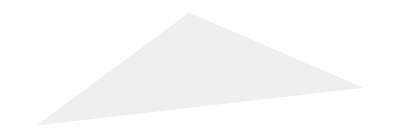

```mathematica
?Graphics
```

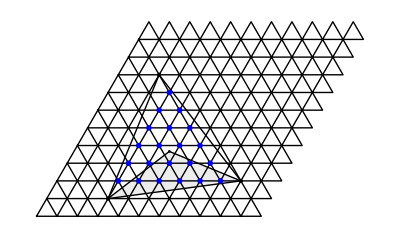

```mathematica
60 17 + 12
```

1032